```mathematica
fanGen={{0,0},{1,0},{0, 1},{-1,-1}};
```

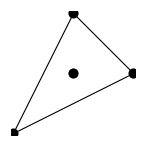

```mathematica
Graphics[{EdgeForm[Black],FaceForm[],Polygon@fanGen[[2;;]], PointSize[.05],Point@fanGen}]
```

```mathematica
fanV = ArrayPad[fanGen, {{0,0}, {0,1}}, 1]
```

{{0,0,1},{1,0,1},{0,1,1},{-1,-1,1}}

```mathematica
Solve[Thread[fanVᵀ.Array[a,4]==0], Array[a,4], Integers]
fanQ = Array[a,4]/.First[%]/.{{C[1]->-1}}
fanVQ = Join[fanVᵀ, %]ᵀ;
fanVQ//MatrixForm
```

{{a[1]→ConditionalExpression[3 C[1], C[1]∈ℤ],a[2]→ConditionalExpression[-C[1], C[1]∈ℤ],a[3]→ConditionalExpression[-C[1], C[1]∈ℤ],a[4]→ConditionalExpression[-C[1], C[1]∈ℤ]}}

{{-3,1,1,1}}

(0 | 0 | 1 | -3
1 | 0 | 1 | 1
0 | 1 | 1 | 1
-1 | -1 | 1 | 1)

```mathematica
CSMDef = Thread[Array[z,Length[fanQ]]->Table[Product[a[i]^fanQ[[A, i]], {i,Length[fanQ[[1]]]}], {A, Length[fanQ]}]]
```

{z[1]→(a[2] a[3] a[4])/a[1]^3}

```mathematica
H[X_,Y_]=Sum[a[i]X^fanVQ[[i,1]]Y^fanVQ[[i,2]], {i,Length[fanVQ]}]
```

a[1]+X a[2]+Y a[3]+a[4]/(X Y)

```mathematica
H[X,Y]/a[1]/.{X->xc X, Y->yc Y}//Expand
H1[X_,Y_]=%/.{xc->a[1]/a[2], yc->a[1]/a[3]}/.{(a[2] a[3] a[4])/a[1]^3->z[1]}
```

1+(X xc a[2])/a[1]+(Y yc a[3])/a[1]+a[4]/(X xc Y yc a[1])

1+X+Y+z[1]/(X Y)

```mathematica
D[f[a[1],a[2],a[3],a[4]], a[2],a[3],a[4]]-D[f[a[1],a[2],a[3],a[4]], {a[1],3}]/.{f[a1_,a2_,a3_,a4_]:>ft[a2 a3 a4/a1^3]}
```

f^(0,1,1,1)[a[1],a[2],a[3],a[4]]-f^(3,0,0,0)[a[1],a[2],a[3],a[4]]

```mathematica
ClearAll[PF1];
PF1[ft_]=a1^3 (D[ft[a2 a3 a4/a1^3], a2,a3,a4]-D[ft[a2 a3 a4/a1^3], {a1,3}])/.{a2->z a1^3/a3/a4}//FullSimplify
```

(1+60 z) ft'[z]+z (3 (1+36 z) ft''[z]+z (1+27 z) ft^(3)[z])

```mathematica
om0 = Series[Log[z]+Plus@@Array[a[#]z^#&, 6], {z, 0, 10}]
```

Log[z]+a[1] z+a[2] z^2+a[3] z^3+a[4] z^4+a[5] z^5+a[6] z^6+O[z]^11

```mathematica
PF1[Function[z, Evaluate[om0]]]/.{a[1]->-6, a[2]->360/8, a[3]->-15120/27,a[4]->554400/64}
```

(18918900+125 a[5]) z^4+(4080 a[5]+216 a[6]) z^5+6840 a[6] z^6+O[z]^10

```mathematica
sol1 ={a[1]->-6, a[2]->360/8, a[3]->-15120/27,a[4]->554400/64};
om0/.sol1//Simplify
```

Log[z]-6 z+45 z^2-560 z^3+(17325 z^4)/2+a[5] z^5+a[6] z^6+O[z]^11

```mathematica
om1 = Series[Log[z]^2+Log[z]om0+Plus@@Array[a[#]z^#&, 6], {z, 0, 10}]
PF1[Function[z, Evaluate[om1]]]
```

2 Log[z]^2+(a[1]+a[1] Log[z]) z+(a[2]+a[2] Log[z]) z^2+(a[3]+a[3] Log[z]) z^3+(a[4]+a[4] Log[z]) z^4+(a[5]+a[5] Log[z]) z^5+(a[6]+a[6] Log[z]) z^6+O[z]^11

(4 a[1]-432 (-1+Log[z])+240 Log[z]+a[1] Log[z]+108 (-3+2 Log[z]))+(81 a[1]+5 a[2]+2 a[2] Log[z]+60 (2 a[1]+a[1] Log[z])+3 (5 a[2]+2 a[2] Log[z])) z+(54 a[2]+21 a[3]+9 a[3] Log[z]+60 (3 a[2]+2 a[2] Log[z])+108 (5 a[2]+2 a[2] Log[z])+3 (11 a[3]+6 a[3] Log[z])) z^2+(5 a[4]+4 a[4] Log[z]+60 (4 a[3]+3 a[3] Log[z])+108 (11 a[3]+6 a[3] Log[z])+27 (17 a[3]+6 a[3] Log[z])+3 (19 a[4]+12 a[4] Log[z])+2 (25 a[4]+12 a[4] Log[z])) z^3+(113 a[5]+65 a[5] Log[z]+60 (5 a[4]+4 a[4] Log[z])+108 (19 a[4]+12 a[4] Log[z])+54 (25 a[4]+12 a[4] Log[z])+3 (29 a[5]+20 a[5] Log[z])) z^4+(7 a[6]+6 a[6] Log[z]+60 (6 a[5]+5 a[5] Log[z])+108 (29 a[5]+20 a[5] Log[z])+27 (107 a[5]+60 a[5] Log[z])+3 (41 a[6]+30 a[6] Log[z])+2 (97 a[6]+60 a[6] Log[z])) z^5+(60 (7 a[6]+6 a[6] Log[z])+108 (41 a[6]+30 a[6] Log[z])+54 (97 a[6]+60 a[6] Log[z])) z^6+O[z]^10

```mathematica
z^r Normal[om0]/.sol1//Expand
D[%, r]/.{r->0}//Simplify
```

-6 z^(1+r)+45 z^(2+r)-560 z^(3+r)+(17325 z^(4+r))/2+z^(5+r) a[5]+z^(6+r) a[6]+z^r Log[z]

Log[z] (-6 z+45 z^2-560 z^3+(17325 z^4)/2+z^5 a[5]+z^6 a[6]+Log[z])

```mathematica
Table[(3n)!/n!^3, {n, 10}]
```

{6,90,1680,34650,756756,17153136,399072960,9465511770,227873431500,5550996791340}

```mathematica
Integrate[(X+Y+z/X/Y)^n /X /Y, {X,0, 1}, {Y,0, 1}]
```

$Aborted

```mathematica
PF2[f_, z_]:=z D[z D[z D[f, z], z], z]-z(3D[3D[3D[f, z]+3, z]+2, z]+1);
```

```mathematica
Log[z]+Sum[a[i]z^i, {i, 1, 12}]
om0 = Series[%, {z, 0, 10}]
```

z a[1]+z^2 a[2]+z^3 a[3]+z^4 a[4]+z^5 a[5]+z^6 a[6]+z^7 a[7]+z^8 a[8]+z^9 a[9]+z^10 a[10]+z^11 a[11]+z^12 a[12]+Log[z]

Log[z]+a[1] z+a[2] z^2+a[3] z^3+a[4] z^4+a[5] z^5+a[6] z^6+a[7] z^7+a[8] z^8+a[9] z^9+a[10] z^10+O[z]^11

```mathematica
PF2[1, z]
```

-z

```mathematica
PF2[om0, z]
```

-54/z^2+(-1+a[1]-162 a[3]) z+(8 a[2]-648 a[4]) z^2+(27 a[3]-1620 a[5]) z^3+(64 a[4]-3240 a[6]) z^4+(125 a[5]-5670 a[7]) z^5+(216 a[6]-9072 a[8]) z^6+(343 a[7]-13608 a[9]) z^7+(512 a[8]-19440 a[10]) z^8+O[z]^9

## Periods from Gamma solution

```mathematica
Gamma/@(fanQᵀ.{(n+r)}+1)
(z)^n/Times@@%
%/.{Gamma[1-3 (n+r)]->Pi(3 (n+r))/Sin[Pi (3 (n+r))]/Gamma[1+3 (n+r)]}
FullSimplify[D[%, {r, 2}]/.{r->0}, n∈PositiveIntegers]
Join[{Limit[%, n->0]}, Table[%, {n, 1, 5}]]
```

{Gamma[1-3 (n+r)],Gamma[1+n+r],Gamma[1+n+r],Gamma[1+n+r]}

z^n/(Gamma[1+n+r]^3 Gamma[1-3 (n+r)])

(z^n Gamma[1+3 (n+r)] Sin[3 π (n+r)])/(3 π (n+r) Gamma[1+n+r]^3)

-(2 (-z)^n (3 n)! (1+3 n HarmonicNumber[n]-3 n HarmonicNumber[3 n]))/(n^5 Gamma[n]^3)

{-∞,-18 z,(423 z^2)/2,-2972 z^3,(389415 z^4)/8,-(21981393 z^5)/25}

```mathematica
Gamma/@(fanQᵀ.{(n+r)}+1)
(z)^n/Times@@%/.{r->0}
Table[%,  {n, 0, 4}]
```

{Gamma[1-3 (n+r)],Gamma[1+n+r],Gamma[1+n+r],Gamma[1+n+r]}

z^n/(Gamma[1-3 n] Gamma[1+n]^3)

{1,0,0,0,0}

```mathematica
Gamma/@(fanQᵀ.{(n+r)}+1)
(z)^(n+r)/Times@@%
%/.{Gamma[1-3 (n+r)]->Pi(3 (n+r))/Sin[Pi (3 (n+r))]/Gamma[1+3 (n+r)]}
FullSimplify[D[%, {r, 2}]/.{r->0}, n∈PositiveIntegers]
Join[{Limit[%, n->0]}, Table[%, {n, 1, 5}]]
```

{Gamma[1-3 (n+r)],Gamma[1+n+r],Gamma[1+n+r],Gamma[1+n+r]}

z^(n+r)/(Gamma[1+n+r]^3 Gamma[1-3 (n+r)])

(z^(n+r) Gamma[1+3 (n+r)] Sin[3 π (n+r)])/(3 π (n+r) Gamma[1+n+r]^3)

-(2 (-z)^n (3 n)! (1+3 n HarmonicNumber[n]-n (3 HarmonicNumber[3 n]+Log[z])))/(n^5 Gamma[n]^3)

{-∞,12 z (-3/2-Log[z]),-45 z^2 (10-2 (147/20+Log[z])),1120/3 z^3 (35/2-3 (7129/840+Log[z])),-17325/4 z^4 (26-4 (86021/9240+Log[z])),1513512/25 z^5 (141/4-5 (1195757/120120+Log[z]))}

## mirror curve analysis

```mathematica
meq=1+X+Y+z/(X Y)
```

1+X+Y+z/(X Y)

```mathematica
Expand[X Y meq]
y1=Y/.Last@Solve[%==0,Y]
```

X Y+X^2 Y+X Y^2+z

(-X-X^2+√X √(X+2 X^2+X^3-4 z))/(2 X)

```mathematica
m1={y->2X Y+X+X^2, x->X};
```

```mathematica
m2=First@Solve[({x,y}/.m1)=={x,y},{X,Y}]
```

{X→x,Y→(-x-x^2+y)/(2 x)}

```mathematica
f4=y^2/.m1/.{Y->y1}/.m2//Expand
Factor@Discriminant[%, x]
```

x^2+2 x^3+x^4-4 x z

-256 z^3 (1+27 z)

```mathematica
Factor[f4/.{z->-1/27}]
```

1/27 x (1+3 x)^2 (4+3 x)

```mathematica
x(4+3 x)-f[t]^2
```

x (4+3 x)-f[t]^2